# Lab 4: Resonant Harmonic Motion Christopher Greene, Michael Imbimbo, Henry Davis

## Simulation 1

0.429

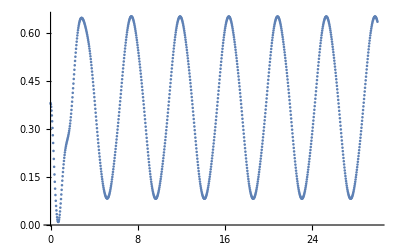

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.5;
y1 = 2.069;
y3 = 0.5246;
xeq=0.366;
vx=0.0;
ti = 0.33;
tf = 0.7705;
dt = .01;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω01 = 1.405;
ϕ=3.733;
b=0.2596;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω01*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim1.csv",modeldata]
```

Sim1.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim1.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar1 = 0.2788;
ϕr1 = 3.861;
ωr1 = 1.405;
```

## Simulation II

0.429

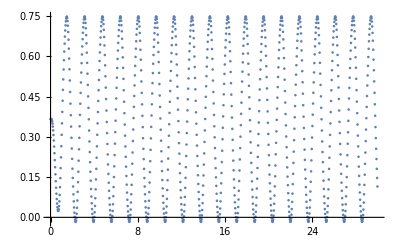

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
xeq=0.366;
x=xeq;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω02 = 3.824;
ϕ=3.082;
b=0.2582;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω02*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim2.csv",modeldata]
```

Sim2.csv

```mathematica
Ar2 = 0.3793;
ϕr2 = 2.266;
ωr2 = 3.824;
```

## Simulation III

0.429

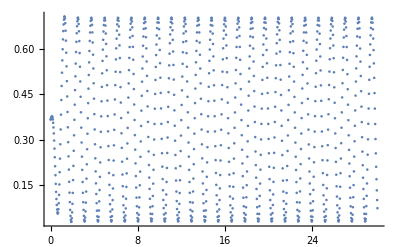

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
xeq=0.366;
x=xeq;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω03 = 5.124;
ϕ=2.813;
b=0.2641;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω03*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim3.csv",modeldata]
```

Sim3.csv

```mathematica
Ar3 = 0.3347;
ϕr3 = 1.320;
ωr3 = 5.124;
```

Follow the same pattern for the rest of the trials.  Make sure that you do the sine fit for late time data (so that the weirdness of the beginning doesn’t make the fit worse.)  After all 10 trials are done, we need to plot ω0 vs ωr, Ar vs ω0, and ϕr vs ω0.  To get the value for b, you do a Sine fit of the angle plot (blue) in the trial data files.  Section 3.6 in the book is what we are doing, so the plots hopefully will look similar to those. *)

## Simulation IV

0.429

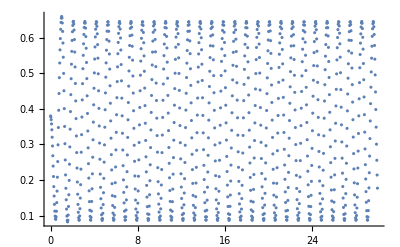

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω04 = 5.935;
ϕ=3.628;
b=0.2547;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω04*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim4.csv",modeldata]
```

Sim4.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim4.csv"]]]
```

AbsoluteFileName::fdnfnd: Directory or file Sim4.csv not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar4 = 0.2786;
ϕr4 = 1.799;
ωr4 = 5.935;
```

## Simulation V

0.429

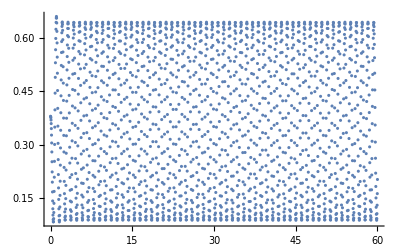

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 60;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω05 = 5.935;
ϕ=3.263;
b=0.2549;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω05*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim5.csv",modeldata]
```

Sim5.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim5.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar5 = 0.2787;
ϕr5 = 1.415;
ωr5 = 5.935;
```

## Simulation VI

0.429

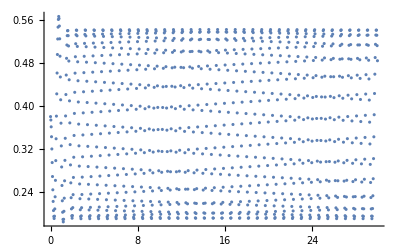

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω06 = 7.765;
ϕ=4.388;
b=0.2613;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω06*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim6.csv",modeldata]
```

Sim6.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim6.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar6 = 0.1767;
ϕr6 = 1.947;
ωr6 = 7.765;
```

## Simulation VII

0.429

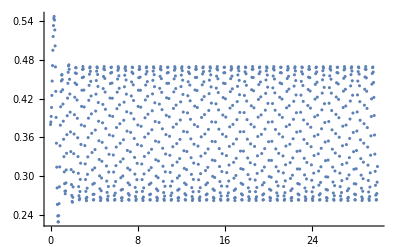

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω07 = 9.686;
ϕ=0.724;
b=0.2572;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω07*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim7.csv",modeldata]
```

Sim7.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim7.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar7 = 0.1034
ϕr7 = 4.129;
ωr7 = 9.686;
```

0.1034

## Simulation VIII

0.429

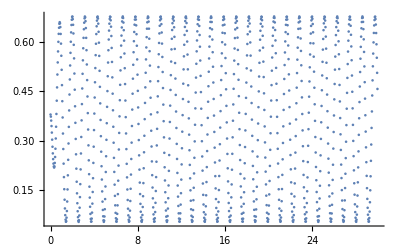

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω08= 5.428;
ϕ=4.982;
b=0.2545;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω08*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim8.csv",modeldata]
```

Sim8.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim8.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar8 = 0.3102;
ϕr8 = 5.428;
ωr8 = 3.350;
```

## Simulation IX

0.429

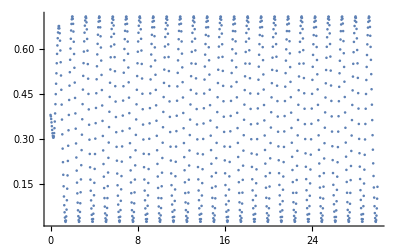

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω09 = 5.077;
ϕ=5.527;
b=0.2667;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω09*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim9.csv",modeldata]
```

Sim9.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim9.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar9 = 0.3391;
ϕr9 = 4.055;
ωr9 = 5.077;
```

## Simulation X

0.429

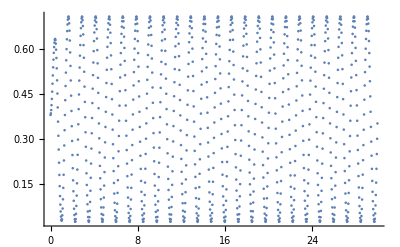

```mathematica
(* define constants and initial conditions *)

g = 9.8;
m = 0.429
x= 0.38;
xeq=0.366;
vx=0.0;
ti = 0;
tf = 30;
dt = .03;
keff = 11.58;
c2 =1.227;
r = 0.12;
ω010= 5.036;
ϕ=1.107;
b=0.2639;
A=b*r;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-(xeq+b*Sin[ω010*t+ϕ]));
Ff2=-Sign[vx ]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Export["Sim10.csv",modeldata]
```

Sim10.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Sim10.csv"]]]
```

After importing the data into LoggerPro, we fit the data to a Sine curve to get the response values of A, ϕ, and ωr

```mathematica
Ar10 = 0.3397;
ϕr10 = 5.938;
ωr10 = 5.036;
```

## Plots of Data

```mathematica
Ar = {Ar1,Ar2,Ar3,Ar4,Ar5,Ar6,Ar7,Ar8,Ar9,Ar10};
ϕr = {ϕr1,ϕr2,ϕr3,ϕr4,ϕr5,ϕr6,ϕr7,ϕr8,ϕr9,ϕr10};
ω0 = {ω01,ω02,ω03,ω04,ω05,ω06,ω07,ω08,ω09,ω010};
ωr = {ωr1,ωr2,ωr3,ωr4,ωr5,ωr6,ωr7,ωr8,ωr9,ωr10};
```

```mathematica
data1 = Transpose@{ω0,Ar};
```

```mathematica
data2 = Transpose@{ω0,ωr};
data3 = Transpose@{ϕr,ω0};
```

Transpose::nmtx: The first two levels of {ω0,ωr} cannot be transposed.

Transpose::nmtx: The first two levels of {ϕr,ω0} cannot be transposed.

Amplitude vs ω0

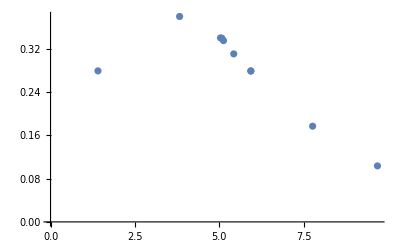

```mathematica
ListPlot[data1]
```

ωr vs ω0

```mathematica
ListPlot[data2]
```

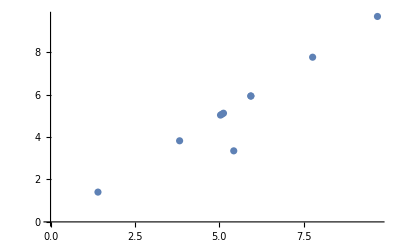

ϕr vs ω0

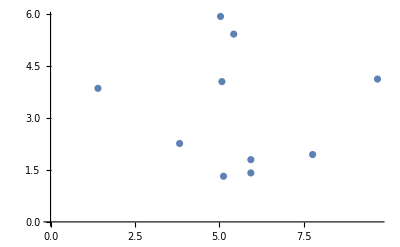

```mathematica
ListPlot[data3]
```